## Bifurcation Plot of Ricker Model

```mathematica
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/seasonal_ews/ricker"];
```

```mathematica
bifData=Import["bif_data.csv"];
```

```mathematica
bifData//Dimensions
```

{101,1001}

```mathematica
bifData[[;;,1]];
```

```mathematica
rVals=bifData[[1,2;;]];
stateVals=bifData[[2;;,2;;]];
```

```mathematica
rVals//Dimensions
```

{1000}

```mathematica
stateVals//Dimensions
```

{100,1000}

```mathematica
stateV
```

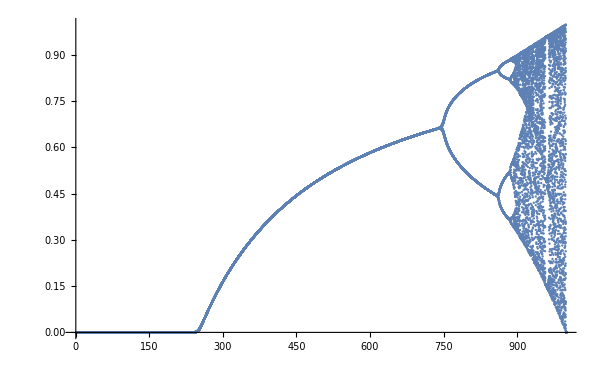

```mathematica
bifPlotMMA=ListPlot[stateVals[[1;;50]],
PlotStyle->TMBcolours[[1]],
ImageSize->600,
LabelStyle->14]
```

```mathematica
Export["images/bifPlotMMA.png",bifPlotMMA,ImageResolution->200];
```